-Graphics-

# The Multiparadigm Data Science Workflow

## Exploratory Data ANALYSIS

## Learning Objectives

Basic tools of Exploratory Data Analysis (EDA)

Statistical exploration

Tukey’s “Five-number summary”: Median, Min, Max, Quartiles

Visual exploration

Basic visualisations

Specialized visualisations

Clustering and outliers

EDA checklist

## Why Do Exploratory Analysis?

Gain an intuitive understanding of the underlying nature of the dataset

Identify relationships between variables

Formulate good questions for the actual analysis (as the explorations proceed, those questions can change)

Evaluate the quality of the data (Data QA)

### Questions to Keep in Mind for EDA

Do you have the data as needed for the planned analysis? Is there enough of it?

Does the data seem to be accurate? Are there obvious errors?

Is the data relevant? Are there outliers?

Is the data missing something?

Are there some characteristics of the features that attract attention right away?

The focus at this stage is completely on the data—its structure, outliers and possible models, irrespective of the type of analysis planned.

## Tools of EDA

EDA tools can be broadly classified into the following categories:

Non-graphical (statistics) or graphical (visualisations)

Univariate (single variable behaviour) or multivariate (combined behaviour of more than one variable—usually two)

### Statistical Explorations

Find descriptive statistics for the features (independent variables) such as:

Minimum & maximum

Median, mean & higher momenta

Quartiles & quantiles

### Visual Explorations

Literally “look” at the data—examine each feature on its own or in comparison with other features with:

Scatter plots, histograms, box plots, …

Bar charts, pie charts, …

Time series plots

Cluster visualisations etc. for single or multiple variables

## Tools for Statistical Explorations

### Case Study: Fisher’s Iris Data

```mathematica
ExampleData[{"Statistics","FisherIris"},"LongDescription"]
```

The data set consists of 50 samples from each of three species of iris flowers.  Four features were measured from each sample, they are the length and the width of sepal and petal. This data set is often used to demonstrate classification techniques and discriminant analysis.

```mathematica
ExampleData[{"Statistics","FisherIris"},"ColumnDescriptions"]
```

### Descriptive Statistics

#### Single variable: Sepal length

This dataset has three classes of flowers. Look at the descriptive statistics (Mean and StandardDeviation) for a single variable (sepal length) for the setosa class:

```mathematica
setosaSampleSepalLengths = Cases[ExampleData[{"Statistics","FisherIris"}],{s_,__,"setosa"}:> s]
```

{5.1,4.9,4.7,4.6,5.,5.4,4.6,5.,4.4,4.9,5.4,4.8,4.8,4.3,5.8,5.7,5.4,5.1,5.7,5.1,5.4,5.1,4.6,5.1,4.8,5.,5.,5.2,5.2,4.7,4.8,5.4,5.2,5.5,4.9,5.,5.5,4.9,4.4,5.1,5.,4.5,4.4,5.,5.1,4.8,5.1,4.6,5.3,5.}

```mathematica
Mean[setosaSampleSepalLengths]
```

```mathematica
StandardDeviation[setosaSampleSepalLengths]
```

The following table visualises the five-number summary (promoted by John Tukey) of the sepal lengths for all three classes:

```mathematica
irisData=ExampleData[{"Statistics","FisherIris"}];
{sepalLengthSetosa, sepalLengthVirginica, sepalLengthVersicolor} =Cases[irisData,{___,#}][[All,1]]& /@ {"setosa","virginica","versicolor"};Grid[Prepend[Transpose[Join[{{"Min","Lower Quartile","Median","Upper Quartile","Max"}},Flatten[{Min[#],Quartiles[#],Max[#]}]&/@{sepalLengthSetosa, sepalLengthVirginica, sepalLengthVersicolor}]],{Style["Species","Text",Gray],Style["Setosa","Text",Red],Style["Virginica","Text",Darker[Green]],Style["Versicolor","Text",Blue]}],Frame->All, Alignment->Left]
```

Species | Setosa | Virginica | Versicolor
Min | 4.3 | 4.9 | 4.9
Lower Quartile | 4.8 | 6.2 | 5.6
Median | 5. | 6.5 | 5.9
Upper Quartile | 5.2 | 6.9 | 6.3
Max | 5.8 | 7.9 | 7.

#### Multivariate data: {sepal length, sepal width, petal length, petal width}

The descriptive statistics (mean and standard deviation) can be computed for more than one variable (sepal length, sepal width, petal length, petal width):

```mathematica
setosaSampleMultivariate = Cases[irisData,{m___,"setosa"}:> {m}]
```

```mathematica
Mean[setosaSampleMultivariate]
```

```mathematica
Variance[setosaSampleMultivariate]
```

The following table visualises the five-number summary for all four features for each of the three classes:

```mathematica
{multivariateSetosa,mutivariateVirginica,multivariateVersicolor} = Cases[irisData,{___,#}][[All,1;;4]]& /@ {"setosa","virginica","versicolor"};Grid[Prepend[Transpose[Join[{{"Min","Lower Quartile","Median","Upper Quartile","Max"}},Column /@{Min /@Transpose[#],Sequence@@Transpose@Quartiles[#],Max/@Transpose[#]}&/@{multivariateSetosa,mutivariateVirginica,multivariateVersicolor} ]],{Style[" ","Text",Gray],Style["Setosa","Text",Red],Style["Virginica","Text",Darker[Green]],Style["Versicolor","Text",Blue]}],Frame->All, Alignment->{{Left,Center,Center,Center}}]
```

| Setosa | Virginica | Versicolor
Min | 4.3
2.3
1.
0.1 | 4.9
2.2
4.5
1.4 | 4.9
2.
3.
1.
Lower Quartile | 4.8
3.2
1.4
0.2 | 6.2
2.8
5.1
1.8 | 5.6
2.5
4.
1.2
Median | 5.
3.4
1.5
0.2 | 6.5
3.
5.55
2. | 5.9
2.8
4.35
1.3
Upper Quartile | 5.2
3.7
1.6
0.3 | 6.9
3.2
5.9
2.3 | 6.3
3.
4.6
1.5
Max | 5.8
4.4
1.9
0.6 | 7.9
3.8
6.9
2.5 | 7.
3.4
5.1
1.8

Can use a resource function instead:

```mathematica
ResourceFunction["StatisticsSummary"][setosaSampleSepalLengths]
```

## Tools for Statistical Explorations

There are a few other numbers that can be useful in understanding the data:

```mathematica
RandomSample[irisData,3]
```

### Frequency Counts

List the number of samples with similar values of sepal lengths:

```mathematica
Counts[Round[irisData[[All,1]]]]//Sort
```

```mathematica
Tally[Round[irisData[[All,1]]]]//Sort
```

### Correlation

Examine the correlation between sepal lengths and petal lengths:

```mathematica
Correlation[irisData[[All,{1,3}]]]//MatrixForm
```

Correlation between all pairs of variables:

```mathematica
Correlation[irisData[[All,1;;4]]]//MatrixForm
```

It seems that features 3 and 4 are strongly correlated, while features 1 and 2 do not show much correlation.

## Tools for Visual Explorations: Scatter Plots

Graphics communicate a lot more than columns of numbers, since humans are highly visual. Human pattern-recognition abilities are therefore better put to use through visual explorations to quickly to check for trends, shapes of distributions, gaps and outliers.

#### Scatter plot: Relationship between two variables—sepal length and sepal width

The correlation between two variables can be visually seen in a scatter plot. Plot the sepal length versus the sepal width for setosa:

```mathematica
setosaSampleSepalLengthsSepalWidths = Cases[irisData,{sl_,sw_,___,"setosa"}:> {sl,sw}]
```

```mathematica
ListPlot[setosaSampleSepalLengthsSepalWidths,AxesLabel->{"sepal length","sepal width"}]
```

The following graphic visualises the relationship between sepal length and sepal width for all three classes:

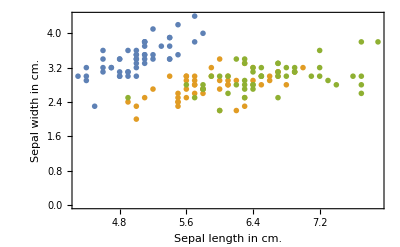

```mathematica
irisData = ExampleData[{"MachineLearning","FisherIris"},"Data"];
{class1,class2,class3} =Keys /@ GatherBy[irisData,Values];
names = #[[1,2]]& /@ GatherBy[irisData,Values];
headers = ExampleData[{"MachineLearning","FisherIris"},"VariableDescriptions"][[1]];
features =StringDrop[#,-7]&/@headers[[1;;4]];
scatter[i_,j_,legends_:None,labels_:None,ticks_:None]:=Module[{pairsOfFeatures},pairsOfFeatures = #[[All,{i,j}]]&/@ {class1,class2,class3} ;
ListPlot[pairsOfFeatures,PlotMarkers->{{Red,6},{Green,6},{Blue,6}},Frame->True,FrameTicks->ticks,PlotLegends->legends,FrameLabel->labels]]
scatter[1,2,names,headers[[{1,2}]],True]
```

#### Scatter plot matrix: Relationships between pairs of variables

A scatter plot matrix shows the pairwise relationship between multiple variables:

```mathematica
variable ={"Sepal length","Sepal width","Petal length","Petal width"};
```

Visualise at a glance how the sepal length corresponds to each of sepal width, petal length and petal width:

```mathematica
ListPlot[setosaSampleMultivariate[[All,{1,#}]],AxesLabel->{variable[[1]],variable[[#]]}]& /@{2,3,4}
```

The preceding comparison repeatedly done for each variable in turn gives the scatter plot matrix:

```mathematica
Table[If[i==j,variable[[i]],ListPlot[setosaSampleMultivariate[[All,{i,j}]]]],{i,4},{j,4}]//Grid
```

The scatter plot matrix following shows the relationships between pairs of variables for all the three classes:

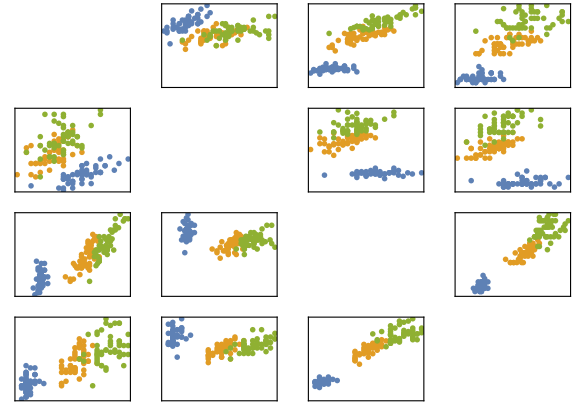

```mathematica
GraphicsGrid[Table[If[i==j,Text[Style[features[[i]],14]],scatter[i,j]],{i,4},{j,4}],ImageSize->Large]
```

## Tools for Visual Exploration: Bar Charts and Pie Charts

### Case Study: Old Faithful Eruptions

```mathematica
ExampleData[{"Statistics","OldFaithful"},"LongDescription"]
```

```mathematica
ExampleData[{"Statistics","OldFaithful"},"ColumnHeadings"]
```

#### Bar charts and pie charts

Focus on the durations of the eruptions.

The duration of eruptions can be grouped and visualised in a bar chart or a pie chart:

```mathematica
ofData=ExampleData[{"Statistics","OldFaithful"}]
```

```mathematica
ofData[[All,1]]
```

Group them into specific bins (less than 2s, more than 2s but less than 3s, etc.):

```mathematica
BinCounts[ofData[[All,1]],{{0,2,3,4,10}}]
```

Visualise the information in a bar chart or pie chart:

```mathematica
BarChart[BinCounts[ofData[[All,1]],{{0,2,3,4,10}}]]
```

```mathematica
PieChart[BinCounts[ofData[[All,1]],{{0,2,3,4,10}}]]
```

Here, the same information is visualised with some labels for ease of use:

```mathematica
{dur,wait}= Transpose[ofData];headers=ExampleData[{"Statistics","OldFaithful"},"ColumnHeadings"];bc=BinCounts[dur,{{0,2,3,4,10}}];GraphicsRow[Table[f[bc,ChartLabels->{"t < 2","2 ≤ t < 3","3 ≤ t < 4","t ≥ 4"}],{f,{BarChart,PieChart}}],ImageSize-> Large]
```

-Graphics-

#### Box plots, violin plots and quantile plots

Some other visualisations that can be helpful in exploring the data:

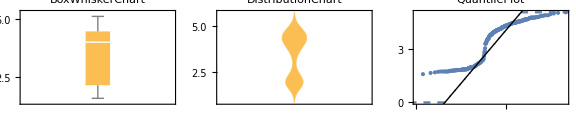

```mathematica
GraphicsGrid[{
Table[f[ofData[[All,1]],PlotLabel->ToString[f]],{f,{BoxWhiskerChart,DistributionChart,QuantilePlot}}]},ImageSize->Large]
```

## Tools for Visual Exploration: Histograms

### Single-Variable Histograms

Histograms are very useful for exploring quantitative variables. They can provide an idea about the shape of distribution for the variable.

For the duration of the eruptions, the Histogram shows two distinct groups:

```mathematica
Histogram[ofData[[All,1]]]
```

The following histograms are shown for the probability density function (PDF) for each variable—duration and wait times:

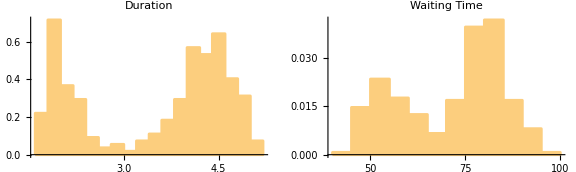

```mathematica
GraphicsRow[{Histogram[ofData[[All,1]],12,"PDF",ChartElementFunction-> "EdgeFadingRectangle",PlotLabel-> Style["Duration","Text"]],Histogram[ofData[[All,2]],12,"PDF",ChartElementFunction-> "EdgeFadingRectangle",PlotLabel-> Style["Waiting Time","Text"]]},ImageSize-> Large]
```

### Paired Histograms

Paired histograms can help compare the distribution of values for both variables. For example, here are two sets of random numbers from two normal distributions, with different means and standard deviations:

```mathematica
rn1 = RandomVariate[NormalDistribution[0,1],100];
rn2 = RandomVariate[NormalDistribution[1,1/2],100];
PairedHistogram[rn1,rn2]
```

To create a similar paired histogram for the Old Faithful data, you need to scale the duration values to be in the same range as the waiting times. The following code creates a paired histogram with scaled durations and unscaled waiting times:

```mathematica
dur =ofData[[All,1]];
wait = ofData[[All,2]];
scaledData=With[{dat1={Min[#],Max[#]}&[dur],dat2={Min[#],Max[#]}&[wait]},Rescale[#,dat1,dat2]&/@dur];
PairedHistogram[scaledData,wait,12,"PDF",ChartLabels-> {Style["Scaled Duration","Text"],Style["Waiting Time","Text"]}]
```

-Graphics-

## Tools for Visual Exploration: Overlaying Graphics

Overlaying plots is useful for comparing a fit with the original data, since humans are better at recognizing deviations from straight lines:

```mathematica
dist = NormalDistribution[0,1];
dataDist = RandomVariate[dist,100];
Show[Histogram[dataDist,10,PDF],Plot[PDF[dist,x],{x,-4,4}]]
```

The following code compares the histogram to an estimated distribution of the wait times:

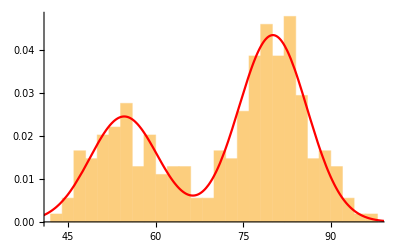

```mathematica
ofDist=EstimatedDistribution[wait,MixtureDistribution[{p1,p2},{NormalDistribution[m1,s1],NormalDistribution[m2,s2]}]];
Show[{Histogram[wait,25,"PDF"],Plot[PDF[ofDist,x],{x,34,100},PlotStyle-> Red]}]
```

## Tools for Visual Exploration: Correlation Plots

It is possible to visualise the multivariate data in 3D through density projections and histograms based on binning or kernel density estimation:

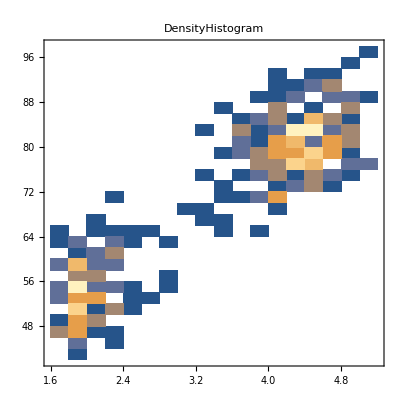

```mathematica
GraphicsGrid[{
{DensityHistogram[ofData,20,"PDF",PlotLabel->"DensityHistogram"],Histogram3D[ofData,20,"PDF",PlotLabel->"Histogram3D"],SmoothHistogram3D[ofData,PlotLabel->"SmoothHistogram3D"]}
},ImageSize->600]
```

## Tools for Visual Exploration: Word Clouds

A WordCloud can give a quick intuitive understanding of frequencies of certain elements in a text piece.

For example, you can get an idea of the most popular registered official languages in countries around the world by creating a word cloud out of the list of languages obtained from CountryData:

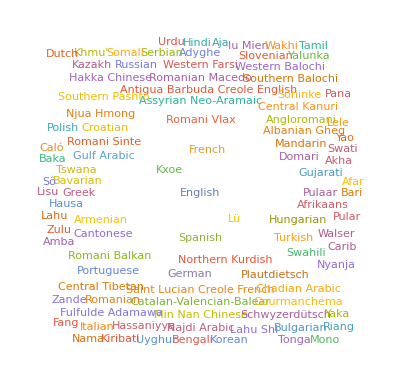

```mathematica
WordCloud[Flatten[CountryData["UN","Languages"]]]
```

## Tools for Visual Exploration: Clustering

Clustering of data is often used to separate data into groups or to try to identify subgroups within a dataset:

```mathematica
clusterData={1.2,9.1,2.3,35.4,35.7,71.8};
FindClusters[clusterData]
```

The following code shows the clustering functions in action using examples of a dataset of dog images:

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"Data","Images"}]];
dogImages=RandomSample[Import/@Flatten[RandomSample[FileNames["*.jpg",#],20]&/@{"n02085620-Chihuahua","n02088238-basset","n02099712-Labrador_retriever"}]];
```

```mathematica
Magnify[FeatureSpacePlot[dogImages],3];
clusters =FindClusters[dogImages,3];
```

## Tools for Visual Exploration: Clustering Visualisations

Create some random data:

```mathematica
colors = RandomColor[30]
```

### ClusteringTree

A weighted tree from the hierarchical clustering of data elements:

```mathematica
ClusteringTree[colors]
```

### Dendrogram

Dendrogram—a tree where the heights of nodes are proportional to intercluster distances:

```mathematica
Dendrogram[colors, ClusterDissimilarityFunction->"Centroid"]
```

## Tools for Visual Exploration: Viewing Data in Feature Space

### FeatureSpacePlot

Intended to automate FeatureExtraction and DimensionReduction—given any collection of objects, FeatureSpacePlot lays them out in an appropriate “feature space” for exploratory analysis.

FeatureSpacePlot uses sophisticated pre-trained feature extractors for specific types of data—like photographs, texts, etc.:

```mathematica
FeatureSpacePlot[{-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-}]
```

## Tools for Visual Exploration: Graphs

Graphs provide great information visualisation. Highlighting graph elements helps information stand out. By using algorithmic graph layouts, much of the structure in a graph, such as connected components, becomes self-evident:

```mathematica
g=ExampleData[{"NetworkGraph","ZacharyKarateClub"}]
```

```mathematica
CommunityGraphPlot[g]
```

### Exercise

#### Visualise a graph of Asian countries that share a border

A graph of the countries in Asia can identify the countries that are most connected (share a border) to other countries (in Asia or other continents).

Here is the map of Asia for reference:

```mathematica
GeoGraphics[Entity["GeographicRegion","Asia"][EntityProperty["GeographicRegion","Countries"]]]
```

-Graphics-

Get “BorderingCountries” from CountryData for Asia and create edge rules of the form Country1 <-> Country2 if Country2 is a bordering country for Country1.

Solution

Use SimpleGraph to create a Graph without duplicate edges. (Graph can be used as well, but it will have two edges for each pair of countries). Use Tooltip for VertexLabels to help identify each country easily.

Solution

Highlight the country with the maximum number of neighbors sharing a border (vertex with greatest DegreeCentrality).

Solution

Explore another graph centrality measure to look for another country that is well-connected to all other countries.

Solution

Find the communities in the graph to see which countries are geographically close together.

Solution

#### Complete solution

Get “BorderingCountries” from CountryData for Asia and create edge rules of the form Country1 <-> Country2 if Country2 is a bordering country for Country1:

```mathematica
Flatten[Thread[#<->CountryData[#,"BorderingCountries"]]&/@CountryData["Asia"]]
```

Use SimpleGraph to create a Graph without duplicate edges. (Graph can be used as well, but it will have two edges for each pair of countries). Use ToolTip for VertexLabels to help identify each country easily:

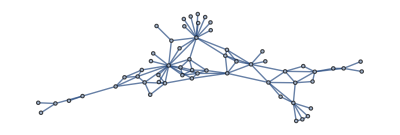

```mathematica
g =SimpleGraph[Flatten[Thread[#<->CountryData[#,"BorderingCountries"]]&/@CountryData["Asia"]],VertexLabels->Placed["Name",Tooltip]]
```

Highlight the country with the maximum number of neighbors sharing a border (vertex with greatest DegreeCentrality):

```mathematica
degreeC = ReverseSort[AssociationThread[VertexList[g]-> DegreeCentrality[g]]]
```

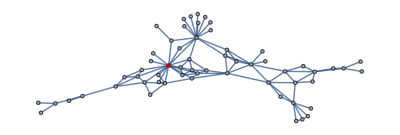

```mathematica
HighlightGraph[g,Keys@Take[degreeC,1]]
```

Explore another graph centrality measure to look for another country that is well-connected to all other countries:

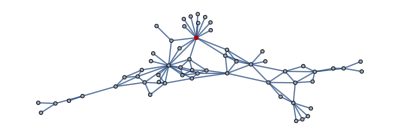

```mathematica
otherC =  ReverseSort[AssociationThread[VertexList[g]-> ClosenessCentrality[g]]];
HighlightGraph[g,Keys@Take[otherC,1]]
```

Find the communities in the graph to see which countries are geographically close together:

```mathematica
CommunityGraphPlot[g]
```

-Graphics-

## Tools for Visual Exploration: Geographics

Superimposing geographically distributed data on maps can provide insight into the relationship of the data with the geography of the place.

Plot the location of earthquakes of magnitudes 7 or higher around the world since 1980:

```mathematica
quakes=EarthquakeData[All,7,{{1980,1,1},{2018,9,30}},"Position"]["Values"]//Quiet;
GeoGraphics[{Red,PointSize[.01],Point[quakes]}]
```

Plot the frequency of such earthquakes around the world:

```mathematica
GeoHistogram[quakes,50,PlotLegends->Automatic]
```

## Tools for Visual Exploration: Visualisations in Time

### DateListPlots

A special type of scatter plot is plots that have time on the x axis and show the change in values of a variable with time on the y axis. These provide insight into the trend of the data.

The following plot shows the daily and weekly mean temperature and humidity of Champaign, IL, in a year:

```mathematica
(*minTemp =WeatherData["KCMI", "MinTemperature", {{2017, 1, 1}, {2018, 1, 1}, "Week"}];
maxTemp =WeatherData["KCMI", "MaxTemperature", {{2017, 1, 1}, {2018, 1, 1}, "Week"}];*)
```

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"data"}]];
Get["ChampaignWeather.mx"]
```

```mathematica
DateListPlot[{minTemp,maxTemp}, Joined->True,Filling->{1->{2}},TargetUnits->"Fahrenheit",PlotStyle->{Dashed,LightBlue,Blue}]
```

Compare it with similar data from a decade earlier:

```mathematica
(*minTemp2007 =WeatherData["KCMI", "MinTemperature", {{2007, 1, 1}, {2008,1, 1}, "Week"}];
maxTemp2007 =WeatherData["KCMI", "MaxTemperature", {{2007, 1, 1}, {2008, 1, 1}, "Week"}];*)
```

```mathematica
DateListPlot[{minTemp,maxTemp,TimeSeriesShift[minTemp2007,{10,"Year"}],TimeSeriesShift[maxTemp2007,{10,"Year"}]}, ]
```

#### Note:

Iconize is helpful in hiding extraneous details from your code:

## Tools for Visual Exploration: Visualisations in Time

### TimelinePlot

TimelinePlot shows when events occur relative to each other:

```mathematica
TimelinePlot[EntityValue[RandomEntity["DeepSpaceProbe",10],"LaunchDate","EntityAssociation"]]
```

The following code creates a TimelinePlot of the earthquakes of varying magnitudes in Asia-Pacific countries in September 2018. It can be used to explore the timeline of occurrence of different magnitude earthquakes in a particular region:

```mathematica
(*earthquakes =GroupBy[{Round[#["Magnitude"]],#["Period"]}&/@ Values[EarthquakeData[Polygon[EntityClass["Country","AsiaPacific"]],All,{{2018,9,1},{2018,9,30}}]],First-> Last]//KeySort;*)
Get["earthquake.mx"];
```

```mathematica
TimelinePlot[Values@ earthquakes,]
```

## Summary

The summary of contents covered in this section can also be used as EDA checklist. Systematically sift through the data and try the following:

Generate summary statistics for each independent variable/feature.

Look at pairwise relationships between variables—correlation and scatter plot matrices.

Plot distributions of all variables. Start with single distribution and single variable, go on to joint distributions of pairs of variables.

Overlay plots and graphs to compare distribution shapes to histograms.

Plot time series of data to see trends in time.

Visualise clusters to identify outliers.

Look for obvious errors or gaps in data plots.

The checklist for EDA should help explore the (real) data collected, identify user stories to make sure the downstream analysis has a real purpose, help formulate the right questions, provide clues about what algorithm to use down the line and tweak your project workflow to include tools identified for use.

Exploratory data analysis, while using many statistical tools, does not comprise any formal statistical modelling and inference.

While similar tools may be used for data visualisation, EDA is done toward the beginning of analysis, while data visualisation is done toward the end to communicate results of analysis. With EDA, the purpose of the graphics is for you to understand what is going on.

## References

Some useful resources on exploratory data analysis:

Chapter on Exploratory Data Analysis from the book Experimental Design and Analysis by Howard J. Seltman.

Exploratory Data Analysis chapter from the NIST/SEMATECH e-Handbook of Statistical Methods.

The Chart Chooser from The Extreme Presentation method by Andrew Abela.

A collection of statistical visualisation functions, with links to more detailed examples, can be found on the Statistical Visualization guide page.

The tutorial Numerical Operations on Data.

For more functions for cluster visualisations, please refer to the collection of functions at Cluster Analysis.

For more information on using Geo* functions, refer to this tutorial on Geographics.